```mathematica
Clear["Global`*"]
```

```mathematica
zdata={{0.,100.},{1.0101010101010102,1.}};
```

```mathematica
z1data={{17.77777777777778,1.},{24.444444444444443,1074.6078283213174},{36.36363636363636,33982.083289425595},{48.484848484848484,115478.19846894582},{60.,153992.6526059492},{72.12121212121212,165481.70999431814},{83.83838383838383,153992.6526059492}};
```

```mathematica
xdata={{0.,100.},{6.936347985215686,11.592473252196486},{12.302765437449594,1.0024042705642937}}
```

{{0.,100.},{6.93635,11.5925},{12.3028,1.0024}}

```mathematica
x1data={{36.16161616161616,1.},{48.282828282828284,191.09529749704407},{60.,3924.1897584845356},{71.91919191919192,7498.942093324558},{84.24242424242424,7498.942093324558}}
```

{{36.1616,1.},{48.2828,191.095},{60.,3924.19},{71.9192,7498.94},{84.2424,7498.94}}

```mathematica
sol1=ParametricNDSolve[{z'[t]==-a z[t],z0'[t]==a z[t]-a0 z0[t],y0'[t]==a0 z0[t-τ0]-γ0 y0[t], y1'[t]==2γ0 y0[t-τ]-γ1 y1[t] ,y2'[t]==2γ1 y1[t-τ]-γ2 y2[t],y3'[t]==2γ2 y2[t-τ]-γ3 y3[t],y4'[t]==2γ3 y3[t-τ]-γ4 y4[t],y5'[t]==2γ4 y4[t-τ]-γ5 y5[t],y6'[t]==2γ5 y5[t-τ]-γ6 y6[t],y7'[t]==2γ6 y6[t-τ]-γ7 y7[t],y8'[t]==2γ7 y7[t-τ]-γ8 y8[t],y9'[t]==2γ8 y8[t-τ]-γ9 y9[t],y10'[t]==2γ9 y9[t-τ]-γ10 y10[t],y11'[t]==2γ10 y10[t-τ]-γ11 y11[t],z1'[t]==γ11 y11[t-τ],z[t/;t≤0]==100,z0[t/;t≤0]==0,y0[t/;t≤0]==0,y1[t/;t≤0]==0,y2[t/;t≤0]==0,y3[t/;t≤0]==0,y4[t/;t≤0]==0,y5[t/;t≤0]==0,y6[t/;t≤0]==0,y7[t/;t≤0]==0,y8[t/;t≤0]==0,y9[t/;t≤0]==0,y10[t/;t≤0]==0,y11[t/;t≤0]==0,z1[t/;t≤0]==0},{z,z0,y0,y1,y2,y3,y4,y5,y6,y7,y8,y9,y10,y11,z1},{t,0,100},{a,a0,γ0,γ1,γ2,γ3,γ4,γ5,γ6,γ7,γ8,γ9,γ10,γ11,τ0,τ}];
```

```mathematica
sol2=ParametricNDSolve[{x'[t]==-a x[t],x0'[t]==a x[t]-a0 x0[t],p0'[t]==a0 x0[t-τ1]-γ0 p0[t], p1'[t]==2γ0 p0[t-τ2]-γ1 p1[t] ,p2'[t]==2γ1 p1[t-τ2]-γ2 p2[t],p3'[t]==2γ2 p2[t-τ2]-γ3 p3[t],p4'[t]==2γ3 p3[t-τ2]-γ4 p4[t],p5'[t]==2γ4 p4[t-τ2]-γ5 p5[t],p6'[t]==2γ5 p5[t-τ2]-γ6 p6[t],x1'[t]==γ6 p6[t-τ2],x[t/;t≤0]==100,x0[t/;t≤0]==0,p0[t/;t≤0]==0,p1[t/;t≤0]==0,p2[t/;t≤0]==0,p3[t/;t≤0]==0,p4[t/;t≤0]==0,p5[t/;t≤0]==0,p6[t/;t≤0]==0,x1[t/;t≤0]==0},{x,x0,p0,p1,p2,p3,p4,p5,p6,x1},{t,0,100},{a,a0,γ0,γ1,γ2,γ3,γ4,γ5,γ6,τ1,τ2}];
```

```mathematica
param1=FindMinimum[
Sum[(z[a,a0,γ0,γ1,γ2,γ3,γ4,γ5,γ6,γ7,γ8,γ9,γ10,γ11,τ0,τ][zdata[[i,1]]]-zdata[[i,2]])^2/.sol1,{i,1,Length[zdata]}]+
Sum[(z1[a,a0,γ0,γ1,γ2,γ3,γ4,γ5,γ6,γ7,γ8,γ9,γ10,γ11,τ0,τ][z1data[[i,1]]]-z1data[[i,2]])^2/.sol1,{i,1,Length[z1data]}],
{{a0,.5},{γ0,.5},{γ1,.5},{γ2,.5},{γ3,.5},{γ4,.5},{γ5,.5},{γ6,.5},{γ7,.5},{γ8,.5},{γ9,.5},{γ10,.5},{γ11,.5},{τ0,1},{τ,1}}
]/.a->Log[100]//Quiet
```

{2.39068×10^9,{a0→0.0580097,γ0→1.17307,γ1→0.86161,γ2→0.771521,γ3→0.463586,γ4→0.984888,γ5→0.37409,γ6→0.339927,γ7→0.315395,γ8→0.322296,γ9→0.322932,γ10→0.346278,γ11→0.341315,τ0→0.596722,τ→0.848532}}

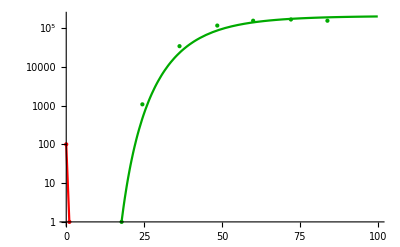

```mathematica
Show[
LogPlot[
Evaluate[{z[a,a0,γ0,γ1,γ2,γ3,γ4,γ5,γ6,γ7,γ8,γ9,γ10,γ11,τ0,τ][t],z1[a,a0,γ0,γ1,γ2,γ3,γ4,γ5,γ6,γ7,γ8,γ9,γ10,γ11,τ0,τ][t]}/.sol1/.Last[param1]/.a->Log[100]],
{t, 0, 100},PlotRange->{{0,100},{1,10^6} },PlotStyle->{Red,Darker[Green]}
],
ListLogPlot[zdata,PlotStyle->Directive[Red,PointSize[Large]]],
ListLogPlot[z1data,PlotStyle->Directive[Darker[Green],PointSize[Large]]],PlotRange->All
]
```

```mathematica
param2=FindMinimum[
Sum[(x[a,a0,γ0,γ1,γ2,γ3,γ4,γ5,γ6,τ1,τ2][xdata[[i,1]]]-xdata[[i,2]])^2/.sol2,{i,1,Length[xdata]}]+
Sum[(x1[a,a0,γ0,γ1,γ2,γ3,γ4,γ5,γ6,τ1,τ2][x1data[[i,1]]]-x1data[[i,2]])^2/.sol2,{i,1,Length[x1data]}],
{{a0,.5},{γ0,.5},{γ1,.5},{γ2,.5},{γ3,.5},{γ4,.5},{γ5,.5},{γ6,.5},{τ1,10},{τ2,3}}
]/.a->Log[100]/12//Quiet
```

{3.95932×10^6,{a0→0.367783,γ0→0.276835,γ1→0.381831,γ2→0.325107,γ3→0.396764,γ4→0.374994,γ5→0.358675,γ6→0.336308,τ1→10.0128,τ2→3.15348}}

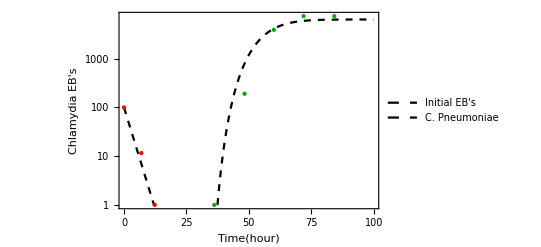

```mathematica
Show[
LogPlot[
Evaluate[{x[a,a0,γ0,γ1,γ2,γ3,γ4,γ5,γ6,τ1,τ2][t],x1[a,a0,γ0,γ1,γ2,γ3,γ4,γ5,γ6,τ1,τ2][t]}/.sol2/.Last[param2]/.a->Log[100]/12],
{t, 0, 100},PlotRange->{{0,100},{1,10^6} },PlotLegends->Placed[{"Initial EB's","C. Pneumoniae"},Above],PlotStyle->{Directive[Black,Dashed],Directive[Black,Dashed]},Frame->{True, True, False,False},FrameLabel->{"Time(hour)","Chlamydia EB's"}
],
ListLogPlot[xdata,PlotStyle->Directive[Red,PointSize[Large]]],
ListLogPlot[x1data,PlotStyle->Directive[Darker[Green],PointSize[Large]]],PlotRange->All
]
```

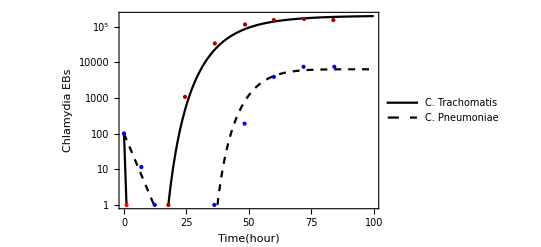

```mathematica
Show[
LogPlot[
{Evaluate[z[Log[100],a0,γ0,γ1,γ2,γ3,γ4,γ5,γ6,γ7,γ8,γ9,γ10,γ11,τ0,τ][t]/.sol1/.Last[param1]],
Evaluate[x[Log[100]/12,a0,γ0,γ1,γ2,γ3,γ4,γ5,γ6,τ1,τ2][t]/.sol2/.Last[param2]],Evaluate[z1[Log[100],a0,γ0,γ1,γ2,γ3,γ4,γ5,γ6,γ7,γ8,γ9,γ10,γ11,τ0,τ][t]/.sol1/.Last[param1]],Evaluate[x1[Log[100]/12,a0,γ0,γ1,γ2,γ3,γ4,γ5,γ6,τ1,τ2][t]/.sol2/.Last[param2]]},
{t, 0, 100},PlotRange->{{0,100},{1,10^6} },PlotLegends->Placed[{"C. Trachomatis","C. Pneumoniae"},Above],AxesStyle->{Black,Thick},PlotTheme->"BoldLabels"
,LabelStyle->Directive[Bold,FontSize->12],PlotStyle->{Directive[Black,Thick],Directive[Black,Dashed],Directive[Black,Thick],Directive[Black,Dashed]},Frame->{True, True, False,False},FrameLabel->{"Time(hour)","Chlamydia EBs"}
],
ListLogPlot[zdata,PlotStyle->Directive[Red,PointSize[Large]]],
ListLogPlot[z1data,PlotStyle->Directive[Darker[Red],PointSize[Large]]],
ListLogPlot[xdata,PlotStyle->Directive[Blue,PointSize[Large]]],
ListLogPlot[x1data,PlotStyle->Directive[Blue,PointSize[Large]]],
PlotRange->All
]
```